## 3.029 Data-Viz Hour 03/29/2022

Scientific Data Link:

https://www.nature.com/articles/s41597-019-0033-6

## Nobel Laureates Dataset

4 datasets

One accumulated one

One for each of Medicine, Physics, and Chemistry with more details

```mathematica
rawData=Import["/home/george/Downloads/Prize-winning paper record.csv","Data"];
headings=First[rawData]
rawData=Rest[rawData];
```

{Field,Laureate ID,Laureate name,Prize year,Title,Pub year,Paper ID,Additional information}

First, group dataset by Field

```mathematica
groupedByField=GroupBy[rawData,First];
Length/@groupedByField
```

<|Physics→283,Chemistry→259,Medicine→332|>

This is odd, presumably this suggests that Medicine is more collaborative (since multiple people share the award every year)

Note: Nobel prizes are awarded to up to three people a year per field

To investigate this, we’ll further group by year

```mathematica
groupedByFieldAndYear=GroupBy[rawData,{First,#[[4]]&}];
Length@*Keys/@groupedByFieldAndYear
```

<|Physics→103,Chemistry→97,Medicine→91|>

That’s curious, they don’t all seem to be awarded on similar years

Let’s investigate further

```mathematica
MinMax@*Keys/@groupedByFieldAndYear
```

<|Physics→{1902,2016},Chemistry→{1908,2016},Medicine→{1912,2016}|>

This explains part of it, but still doesn’t add up

```mathematica
nobelTimelines=TimelinePlot[Interval/@Map[DateObject[{#}]&,Sort[MinMax/@Split[Keys[#],#1-#2==1&]],{2}]&/@groupedByFieldAndYear]
```

-Graphics-

```mathematica
wars=Interval/@EntityValue[EntityList[FilteredEntityClass["MilitaryConflict",EntityFunction[conflict,conflict["StartDate"]>=DateObject[{1902,1,1},"Day"]&&conflict["EndDate"]<=DateObject[{2016,31,12},"Day"]]]],{"StartDate","EndDate"}];
```

GreaterEqual::nordol: DateObject[{1902},Year] and DateObject[{1902,1,1},Day] cannot be compared because they are overlapping.

```mathematica
TimelinePlot[wars[[;;1000]],PlotLayout->"Overlapped"]
```

-Graphics-

Not super insightful

other than as commentary on the state of the world

```mathematica
yearsFromPublicationToAward=Select[Subtract@@@rawData[[All,{4,6}]],Positive];
```

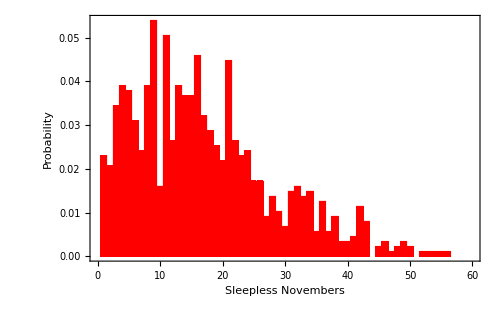

```mathematica
histogram=Histogram[yearsFromPublicationToAward,50,"Probability",PlotRange->{{0,60},All},Frame->True,BaseStyle->18,ChartStyle->Red,FrameStyle->Directive[Black,Thick],ImageSize->500,FrameLabel->{"Sleepless Novembers","Probability"}]
```

```mathematica
Mean[yearsFromPublicationToAward]//N
StandardDeviation[yearsFromPublicationToAward]//N
```

17.0964

11.2174

Let’s guess what this distribution looks like

Perhaps Log-Normal?

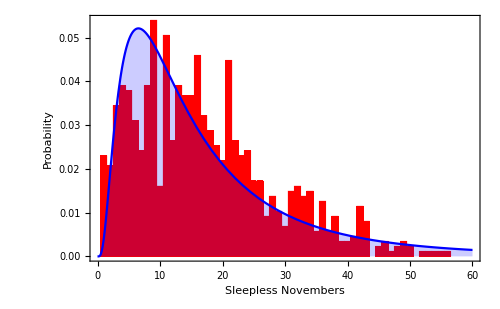

```mathematica
distributionGuess=EstimatedDistribution[yearsFromPublicationToAward,LogNormalDistribution[μ,σ]];
Show[histogram,Plot[PDF[distributionGuess,n],{n,0,60},Filling->Bottom,PlotStyle->Blue]]
```

```mathematica
feynmanPapers=GroupBy[Import["/home/george/Downloads/Physics publication record.csv","Data"]//Rest,First][10119];
```

```mathematica
words=Select[DeleteStopwords[Join@@(StringSplit/@feynmanPapers[[All,4]])],StringLength[#]>4&];
```

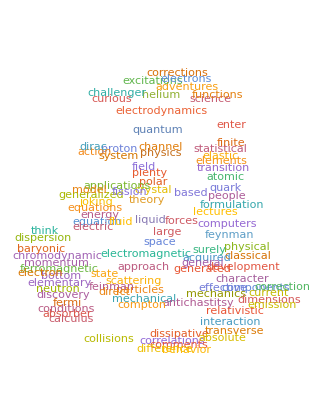

```mathematica
WordCloud[words,MorphologicalBinarize[-Graphics-,0.5]]
```